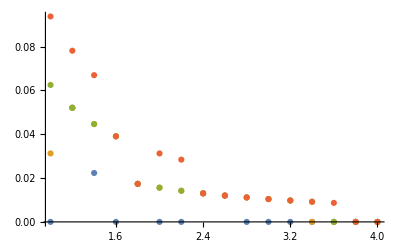

```mathematica
b11={{1,2/(1×32)}, {1.2,5/(1.2×32)},{1.4,12/(1.4×32)},{1.6,20/(1.6×32)}, {1.8,26/(1.8×32)},{2,34/(2×32)},{2.2,40/(2.2×32)},{2.4,46/(2.4×32)},{2.6,53/(2.6×32)},{2.8,60/(2.8×32)},{3,67/(3×32)},{3.2,73/(3.2×32)},{3.4,79/(3.4×32)},{3.6,86/(3.6×32)},{3.8,92/(3.8×32)},{4,99/(4×32)}};
b21={{1,4/(1×32)}, {1.2,7/(1.2×32)},{1.4,13/(1.4×32)},{1.6,21/(1.6×32)}, {1.8,28/(1.8×32)},{2,35/(2×32)},{2.2,41/(2.2×32)},{2.4,48/(2.4×32)},{2.6,55/(2.6×32)},{2.8,61/(2.8×32)},{3,68/(3×32)},{3.2,74/(3.2×32)},{3.4,81/(3.4×32)},{3.6,88/(3.6×32)},{3.8,94/(3.8×32)},{4,101/(4×32)}};
b31={{1,6/(1×32)}, {1.2,10/(1.2×32)},{1.4,16/(1.4×32)},{1.6,23/(1.6×32)}, {1.8,30/(1.8×32)},{2,37/(2×32)},{2.2,43/(2.2×32)},{2.4,50/(2.4×32)},{2.6,57/(2.6×32)},{2.8,63/(2.8×32)},{3,70/(3×32)},{3.2,76/(3.2×32)},{3.4,82/(3.4×32)},{3.6,90/(3.6×32)},{3.8,96/(3.8×32)},{4,103/(4×32)}};
b41={{1,8/(1×32)}, {1.2,12/(1.2×32)},{1.4,18/(1.4×32)},{1.6,25/(1.6×32)}, {1.8,32/(1.8×32)},{2,39/(2×32)},{2.2,45/(2.2×32)},{2.4,52/(2.4×32)},{2.6,59/(2.6×32)},{2.8,65/(2.8×32)},{3,72/(3×32)},{3.2,78/(3.2×32)},{3.4,84/(3.4×32)},{3.6,91/(3.6×32)},{3.8,98/(3.8×32)},{4,105/(4×32)}};
b12={{1,2/(1×32)}, {1.2,7/(1.2×32)},{1.4,13/(1.4×32)},{1.6,20/(1.6×32)}, {1.8,27/(1.8×32)},{2,34/(2×32)},{2.2,40/(2.2×32)},{2.4,47/(2.4×32)},{2.6,54/(2.6×32)},{2.8,60/(2.8×32)},{3,67/(3×32)},{3.2,73/(3.2×32)},{3.4,79/(3.4×32)},{3.6,86/(3.6×32)},{3.8,92/(3.8×32)},{4,99/(4×32)}};
b22={{1,5/(1×32)}, {1.2,9/(1.2×32)},{1.4,15/(1.4×32)},{1.6,23/(1.6×32)}, {1.8,29/(1.8×32)},{2,36/(2×32)},{2.2,42/(2.2×32)},{2.4,49/(2.4×32)},{2.6,56/(2.6×32)},{2.8,62/(2.8×32)},{3,69/(3×32)},{3.2,75/(3.2×32)},{3.4,81/(3.4×32)},{3.6,88/(3.6×32)},{3.8,94/(3.8×32)},{4,101/(4×32)}};
b32={{1,8/(1×32)}, {1.2,12/(1.2×32)},{1.4,18/(1.4×32)},{1.6,25/(1.6×32)}, {1.8,31/(1.8×32)},{2,38/(2×32)},{2.2,44/(2.2×32)},{2.4,51/(2.4×32)},{2.6,58/(2.6×32)},{2.8,64/(2.8×32)},{3,71/(3×32)},{3.2,77/(3.2×32)},{3.4,83/(3.4×32)},{3.6,90/(3.6×32)},{3.8,96/(3.8×32)},{4,103/(4×32)}};
b42={{1,11/(1×32)}, {1.2,15/(1.2×32)},{1.4,21/(1.4×32)},{1.6,27/(1.6×32)}, {1.8,33/(1.8×32)},{2,41/(2×32)},{2.2,47/(2.2×32)},{2.4,53/(2.4×32)},{2.6,60/(2.6×32)},{2.8,66/(2.8×32)},{3,73/(3×32)},{3.2,79/(3.2×32)},{3.4,85/(3.4×32)},{3.6,92/(3.6×32)},{3.8,98/(3.8×32)},{4,105/(4×32)}};
b1=b12-b11*Table[{0,1},{i,0,15}];
b2=b22-b21*Table[{0,1},{i,0,15}];
b3=b32-b31*Table[{0,1},{i,0,15}];
b4=b42-b41*Table[{0,1},{i,0,15}];
ListPlot[{b1,b2,b3,b4}]
```

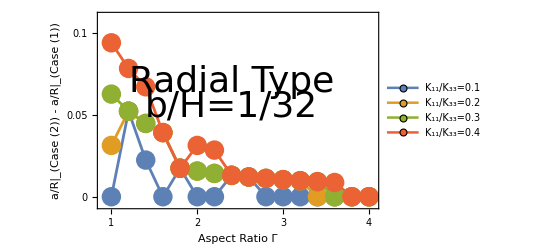

```mathematica
ListPlot[{b1,b2,b3,b4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0,0.05,0.1},None},{{0,1,2,3,4},None}}, PlotRange->{{0.9,4.05},{-0.005,0.11}},FrameLabel->{{"a/R|_(Case (2)) - a/R|_(Case (1))", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Right, Top}],Epilog->{Text[Style["Radial Type",Directive[Black,36]],{2.4,0.07}],Text[Style["b/H=1/32",Directive[Black,36]],{2.4,0.055}]}]
```